```mathematica
a="111111111
100000001
101000101
101000101
100010001
100000001
101111101
100111001
100000001
111111111";
a="1110110110010001110011101110100101111
1010101010101001010010101000101001000
1110101010101001110010101000110001111
1000100010111001010010101000101000001
1000100010101001001011101110100101111";

b=FromDigits[StringReplace[a,"\n"->""],2]
```

45509287084361729171620569523023183098514739809575361839

```mathematica
0.45509287084361729171620569523023183098514739809575361839
```

```mathematica
a=IntegerDigits[b,2]
Length[%]//FactorInteger
```

{1,1,1,0,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,1,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0,1,0,0,1,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1}

{{5,1},{37,1}}

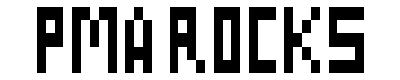

```mathematica
ArrayPlot[Partition[a,37]]
```

```mathematica
k=4858450636189713423582095962494202044581400587983244549483093085061934704708809928450644769865524364849997247024915119110411605739177407856919754326571855442057210445735883681829823754139634338225199452191651284348332905131193199953502413758765239264874613394906870130562295813219481113685339535565290850023875092856892694555974281546386510730049106723058933586052544096664351265349363643957125565695936815184334857605266940161251266951421550539554519153785457525756590740540157929001765967965480064427829131488548259914721248506352686630476300;
```

```mathematica
f[x_,y_]:=1/2<⌊Mod[⌊y/17⌋2^(-17⌊x⌋-Mod[⌊y⌋,17]),2]⌋
ArrayPlot[Table[Table[If[f[x,y-k],1,0],{x,0,105}],{y,17,0,-1}]]
```

```mathematica
a=Fibonacci[123]
b=IntegerDigits[a,2];
l=Length[b]
fs=Take[Divisors[l],{2,-2}]
f=RandomChoice[fs]
ArrayPlot[Partition[b,f]]
```

```mathematica
Table[{ArrayPlot[Partition[RealDigits[1/i,2,120][[1]],11]],i},{i,20,100}]
```

```mathematica
Table[ArrayPlot[Partition[RealDigits[1/97,2,120][[1]],i]],{i,3,50}]
```

```mathematica
i=5
Table[Length[RealDigits[1/i,2][[1,1]]],{i,1,100}]
```

```mathematica
RealDigits[1/97,2]
ClearAll[a]
a[0]={"000","101","101","101","111"};
a[1]={"1","1","1","1","1"};
a[2]={"111","001","111","100","111"};
a[3]={"111","001","111","001","111"};
```

```mathematica
$MinPrecision=100
```

100

```mathematica
b
```

```mathematica
d=4.5509287084361729171620569523023183098514739809575361839
c=N[11/6 Pi Cot[6523795/7728277]^2,100]
```

```mathematica
4.5509287084361729 171620569523023183098514739809575361839`100.
```

```mathematica
4.5509287084361729 25677812147585252754639486290514093514849654466120745670727913701360778745224510286023243485054209214756282993977997558`100.
```

```mathematica
4.5509287084361729 2567781214758525275463948629051409351484965446612074567072785`50.
```

Precision::precsm: Requested precision 50. is smaller than $MinPrecision. Using $MinPrecision instead.

1.16858×10^61

```mathematica
c-d
```

8.515755195282934444788012309556557330949654466120745670727913701360778745224510286023243485054209215×10^-18

```mathematica
e=N[(64+913 E-50 E^2)/(-1062+355 E+359 E^2),100] 10^-17
```

8.515755195282934443967533972313757620591591363035101593645619736917037240375898626310148261979809594×10^-18

```mathematica
d
c-e
d-(c-e)
```

4.5509287084361729171620569523023183098514739809575361839

4.55092870843617291716205695230231831067195231820033589425806310308564407708229396444374150484861166

-8.204783372427997103580631030856440770822939644437415048486116597130952230743996208206481405124657734×10^-37

```mathematica
4.5509287084361729171620569523023183 098514739809575361839`100.
```

```mathematica
4.5509287084361729171620569523023183 10671952318200335894258063103085644077082293964443741504848611659713095223074399620820648140512465773`100.
```

```mathematica
f=N[1/2 Sqrt[1/14 (1890+3526 E-3647 Pi-24 Log[2])] ,100] 10^-55
```

1.067195231820032962248273668801731213142070673724522046383309223138468194761616207768212286916408587×10^-56

```mathematica
d-(c-e)
g=FindRoot[9313725 x^3-5144282,{x,-1}, WorkingPrecision->100][[1,2]] 10^-36
```

-8.204783372427997103580631030856440770822939644437415048486116597130952230743996208206481405124657734×10^-37

8.204783372427996516939663551731477039196600751698333736714313269211928228600768290153878846545307725×10^-37

```mathematica
((c-e))-g
d
(d-(c-e))+g
d -(c-e)+g

h=N[(+44)/75 10^-52,100]
```

4.550928708436172917162056952302318309851473980957536242564096747912496373162633889273908131177180333

4.5509287084361729171620569523023183098514739809575361839

-5.866409674791249637316263388927390813117718033279190240021432279180526025585793500094199335672162196×10^-53

-5.866409674791249637316263388927390813117718033279190240021432279180526025585793500094199335672162196×10^-53

5.866666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667×10^-53

```mathematica
d
i=(c-e)-g-h
```

4.5509287084361729171620569523023183098514739809575361839

4.550928708436172917162056952302318309851473980957536183897430081245829706495967222607241464510513666

4.550928708436172917162056952302318309851473980957536183897430081245829706495967222607241464510513666×10^55

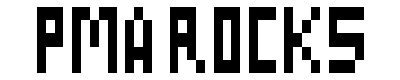

{{1,1,1,0,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,1,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0,1,0,0,1,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,1,0,1,1,1,1,1,0,0,1,0,1,1,0,1,0,1,1,1,1,0,0,0,1,1,1,0,0,1,0,1,1,0,1,1,1,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,0,1,1,0,0,1,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,1,0,0,1,1,1,0,0,0,1,1,0,0,0,1,0,1,0,0,0,0,0,0,1,1,0,1,1,0,1,1,0,0,1,0,1,1,1,1,0,0,1,0,0,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,0},185}

{{1,0,0,1,0,0,0,1,1,0,1,0,0,0,0,1,0,0,1,1,0,1,0,1,0,0,1,1,1,1,1,0,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,1,1,1,1,0,0,1,0,0,0,0,0,1,1,0,0,0,1,0,1,1,1,0,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,1,1,1,1,1,1,1,0,1,0,0,0,1,1,1,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,1,1,0,0,0,0,1,0,1,1,0,1,1,1,1,0,0,0,0,1,0,1,1,0,0,1,1,1,1,0,1,0,0,1,1,0,0,1,0,1,1,1,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,1,1,0,1,1,0,1,1,0,0,0,1,0,0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1,0,1,1,1,0,1,1,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,1,1,1,1,1,0,1,0,1,1,0,1,0,0,1,1,1,1,0,1,0,1,0,1,1,0,1,1,1,0,0,1,1,0,1,1,1,1,1,1,0,0,0,0,1,0,1,1,1,0,0,0,0,1,0,0,1,1,0,1,1,0,0,1,1,0,0,1,0,1,0,1,1},3}

```mathematica
q=i 10^55

ArrayPlot[Partition[RealDigits[%,2,185][[1]],37]]
RealDigits[q,2]
```

```mathematica
IntegerDigits[b,2]
```

{1,1,1,0,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,1,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0,1,0,0,1,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1}

```mathematica
d 10^55
RealDigits[%,2]
```

4.5509287084361729171620569523023183098514739809575361839×10^55

{{1,1,1,0,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,1,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0,1,0,0,1,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},185}